## Frequency Tables

```mathematica
Manipulate[DynamicModule[{weights,frequencies,totalEggs,meanWeight,weightTimesFreq},(*Data preparation-using explicit values rather than calculations that might fail*)weights={44,48,52,56,60};
frequencies={freq44,freq48,freq52,freq56,freq60};
weightTimesFreq={44*freq44,48*freq48,52*freq52,56*freq56,60*freq60};
totalEggs=freq44+freq48+freq52+freq56+freq60;
meanWeight=If[totalEggs>0,N[(44*freq44+48*freq48+52*freq52+56*freq56+60*freq60)/totalEggs,4],0];
Column[{(*Title and instructions*)Panel[Column[{Style["Egg Weight Frequency Distribution",Bold,18,Blue],Style["The frequency table shows the weights of eggs laid by hens on a free range farm.",14],Style["Adjust the sliders to change the frequency of each weight category.",14],Style["Try to calculate the mean weight of the eggs (to 1 decimal place).",14,Bold]},Spacing->1],Background->LightYellow,FrameMargins->15,ImageSize->Full],(*Frequency Table and Visualization in a Grid*)Grid[{{(*Frequency table display*)Panel[Grid[{{Style["Egg Weight (grams)",Bold],Style["Frequency",Bold],Style["Weight × Frequency",Bold]},{44,freq44,44*freq44},{48,freq48,48*freq48},{52,freq52,52*freq52},{56,freq56,56*freq56},{60,freq60,60*freq60},{Style["Total",Bold],totalEggs,Total[weightTimesFreq]}},Dividers->All,Background->{{},{1->LightGreen,7->LightCyan}},Alignment->{{Center,Center,Center},{Center}}],FrameMargins->15],(*Histogram visualization*)Panel[Column[{Style["Visual Distribution",Bold,15],If[totalEggs>0,BarChart[frequencies,ChartLabels->Placed[weights,Below],AxesLabel->{"Egg Weight (g)","Frequency"},PlotTheme->"Detailed",ChartStyle->"Rainbow",ImageSize->400],Text[Style["Please add some eggs using the sliders below.",14,Italic,Red]]]}],FrameMargins->15,ImageSize->450]}},Alignment->Top,Spacings->2],(*Mean calculation section*)Panel[Grid[{{Column[{Style["Calculate the Mean:",Bold,15],"Formula: Mean = (sum of weights × frequencies) ÷ (total frequency)",Dynamic[Button[If[showSolution,"Hide Solution","Show Solution"],showSolution=Not[showSolution],BaseStyle->{15,Bold},ImageSize->150,Background->If[showSolution,LightOrange,LightBlue]]]}],Column[{Style["Statistics:",Bold,15],Grid[{{"Total eggs:",Style[totalEggs,14]},{"Sum of (weight × frequency):",Style[Total[weightTimesFreq],14]},{"Mean weight:",Dynamic[If[showSolution&&totalEggs>0,Style[ToString[NumberForm[meanWeight,{3,1}]]<>" grams",Bold,Red,14],Style["? grams",14]]]}},Alignment->{{Left,Right},Center},Spacings->{2,0.5}]}]}},Alignment->{{Left,Right},Top},Spacings->5],Background->LightCyan,FrameMargins->15,ImageSize->Full],(*Educational notes*)Dynamic[If[showSolution&&totalEggs>0,Panel[Style["Note: The mean weight is calculated by multiplying each weight by its frequency, adding these products, then dividing by the total number of eggs. This gives us the weighted average of all the eggs.",14,Italic],Background->Lighter[Green,0.9],FrameMargins->15,ImageSize->Full],""]]},Spacing->15,Alignment->Center]],(*Individual controls for each frequency-using separate variable names*){{freq44,3,"44g eggs:"},0,15,1,Appearance->"Labeled"},{{freq48,6,"48g eggs:"},0,15,1,Appearance->"Labeled"},{{freq52,8,"52g eggs:"},0,15,1,Appearance->"Labeled"},{{freq56,5,"56g eggs:"},0,15,1,Appearance->"Labeled"},{{freq60,2,"60g eggs:"},0,15,1,Appearance->"Labeled"},{{showSolution,False},None},ControlPlacement->Bottom,SaveDefinitions->True]

(*To deploy to Wolfram Cloud*)
(*CloudDeploy[%,"EggWeightFrequencyTable",Permissions->"Public"]*)
```

```mathematica
CloudObject[["https://www.wolframcloud.com/obj/cb726e98-589c-427b-b01f-ce67faa1ce8c"](https://www.wolframcloud.com/obj/cb726e98-589c-427b-b01f-ce67faa1ce8c)]//DeleteObject
```

## Enlargement

```mathematica
enlargePolygon[vertices_,scaleFactor_,center_]:=Module[{originalPolygon,enlargedPolygon,plotTitle},(*Create the original polygon from vertices*)originalPolygon=ConvexHullMesh[vertices];
(*Create the enlarged polygon using geometric transformation*)enlargedPolygon=GeometricTransformation[originalPolygon,ScalingTransform[{scaleFactor,scaleFactor},center]];
(*Create plot title*)plotTitle="Polygon Enlargement with Scale Factor = "<>ToString[scaleFactor]<>" from Center "<>ToString[center];
(*Determine an appropriate plot range based on original and enlarged vertices*)allPoints=Join[vertices,Table[center+scaleFactor*(vertices[[i]]-center),{i,1,Length[vertices]}],{center}];
xMin=Min[allPoints[[All,1]]]-1;
xMax=Max[allPoints[[All,1]]]+1;
yMin=Min[allPoints[[All,2]]]-1;
yMax=Max[allPoints[[All,2]]]+1;
(*Create and return the plot*)Graphics[{(*Enlarged polygon-slightly transparent*){LightPink,Opacity[0.6],enlargedPolygon},(*Original polygon*){LightOrange,Opacity[1],originalPolygon},(*Center point*){Red,PointSize[0.02],Point[center]},Text["Center: "<>ToString[center],center,{-1,-1}],(*Original vertices*){Green,PointSize[0.015],Point[vertices]},Table[Text["v"<>ToString[i]<>": "<>ToString[vertices[[i]]],vertices[[i]],{0,1}],{i,1,Length[vertices]}],(*Enlarged vertices*){Orange,PointSize[0.015],Point[Table[center+scaleFactor*(vertices[[i]]-center),{i,1,Length[vertices]}]]},(*Connection lines between original and enlarged vertices*){Gray,Dashed,Table[Line[{vertices[[i]],center+scaleFactor*(vertices[[i]]-center)}],{i,1,Length[vertices]}]}},Frame->True,Axes->True,AxesLabel->{"x","y"},AxesStyle->Thick,GridLines->{Range[-100,100,1],Range[-100,100,1]},PlotRange->{{xMin,xMax},{yMin,yMax}},PlotLabel->plotTitle,ImageSize->600]]
(*Deploy a simple form interface*)
CloudDeploy[FormFunction[{"vertices"->"String","center"->"String","scaleFactor"->"Number"},Module[{vertexList,centerPoint},(*Parse the input string of vertices*)vertexList=ToExpression[#vertices];
(*Parse the center point*)centerPoint=ToExpression[#center];
(*Run the function with user inputs*)enlargePolygon[vertexList,#scaleFactor,centerPoint]]&,"PNG"],"SimpleEnlargementTool",Permissions->"Public"]
```

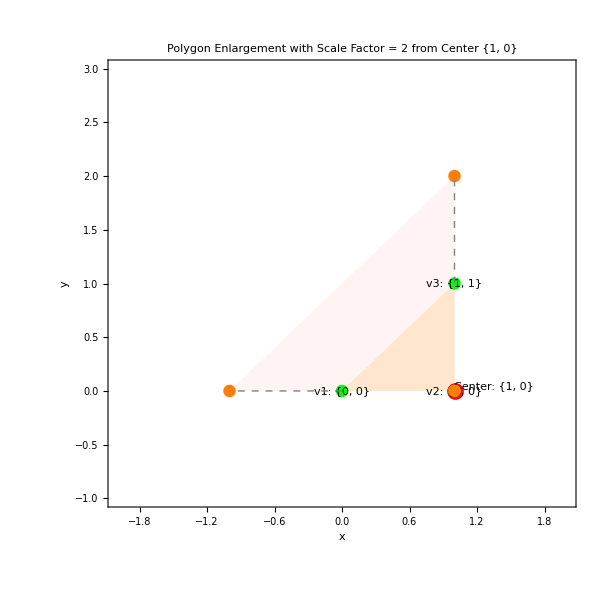

```mathematica
enlargePolygon[{{0,0},{1,0},{1,1}},2,{1,0}]
```